# Data Visualisation: Data Analysis & Creating Interactive Visualisations with Mathematica

```mathematica
-Graphics--Graphics-
```

Both Mathematica and the Wolfram Language are developed and owned by the commercial entity Wolfram Research - the use of both these technologies are subject to their licensing and EULA agreements.

Mathematica is a powerful IDE for using the Wolfram Language to investigate, analyse and visualise data. It is fairly unique in that the UI is generated from intepreted Wolfram Language code and may also be programmatically manipulated using the Wolfram Language.

In general, most users of the Wolfram Language use the Mathematica interface (called the notebook) as it provides a literate programming environment. As we’ll see throught this course, it’s possible to create interactive visualisations within Mathematica notebooks and to share these with others using a variety of technologies that are discussed in the Wolfram Cloud section of this course.

It is possible to use the Wolfram Language through the shell, on a server or remotely on the cloud - this course only considers the desktop Mathematica environment in detail.

# What is this course about?

This course introduces the Wolfram Language and the Mathematica environment from the point of view of an user interested (or experienced) in visualising research data and creating interactive content.

In this course we do not consider the nature of the Wolfram Language from the point of view of a computer programmer and in fact deliberately gloss over functionality required to build generic solutions to programming tasks. It’s advised that you investigate the Wolfram Lnguage and Mathematica Fundamentals course to solidify the knowkedge you develop here.

This course also does not cover the diverse analytical capabilities of the Wolfram Language, for instance its network analysis, machine learning, or analytical calculus functions. Future ITLP course may concentrate on these features if there is sufficient interest.

# Scripting Languages and the Wolfram Language

The Wolfram Language is an example of a scripting language, for our purposes a scripting language is defined as follows:

Scripting languages allow users to write code that automate tasks in a “read-eval-print” loop, do not require a deep understanding of computer science and typically provide a wide array of libraries of built-in functions for performing complex operations in a simple way. Often without understanding the specifics of the alogorithm or underlying mathematica principles.

Scripting languages include:

Python

R

Wolfram Language

## The Wolfram Language

The Wolfram Language is fairly unique in the scripting languages in that it was originally designed for solving calculus and algebraic problems.

It is therefore often described as a symbolic language which provides two benefits to all users

Mathematical problems can be solved directly and simply

```mathematica
Solve[{4*x^2+x+2==0},x]
```

Output can be represented symbolically, allowing the user to understand how expressions are evaluated

```mathematica
NestList[#+b^#&,1,3]
```

Other scripting languages have a broad community of users who contribute small, dedicated packages/libraries for specific functionality, for instance in R there is library called lubridate that is incredibly useful for handling dates.

In the case of the Wolfram Language, the vast majority of functionality is developed by Wolfram Research and built into the product. This is often an advantage as functions work together seemlessly and handle multiple data types, however there is a disadvantage in the inner workings of functions often being unavailable to the end user.

```mathematica
digit=Classify[
{-Graphics-->2,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->2,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->9,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->2,-Graphics-->0,-Graphics-->6,-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->7,-Graphics-->8,-Graphics-->5,-Graphics-->0,-Graphics-->4,-Graphics-->7,-Graphics-->6,-Graphics-->0,-Graphics-->2,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->4,-Graphics-->1,-Graphics-->9,-Graphics-->3,-Graphics-->6,-Graphics-->8,-Graphics-->0,-Graphics-->9,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->7,-Graphics-->4,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->0,-Graphics-->4,-Graphics-->1,-Graphics-->3,-Graphics-->7,-Graphics-->6,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->7,-Graphics-->2,-Graphics-->5,-Graphics-->2,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->9,-Graphics-->8,-Graphics-->1,-Graphics-->6,-Graphics-->4,-Graphics-->8,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->6,-Graphics-->7,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->1,-Graphics-->9,-Graphics-->9,-Graphics-->9,-Graphics-->2,-Graphics-->4,-Graphics-->7,-Graphics-->3,-Graphics-->1,-Graphics-->9,-Graphics-->2,-Graphics-->9,-Graphics-->6}];
digit[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,1,2,3,4,1,4,7,8,9}

This course will not explore these capabilities or further compare the Wolfram Language to other scripting languages. However it is useful to understand from the outset of learning a language what it is useful for and how it differs from other languages.

# Five Things You Need to Know

To use the Mathematica environment there are five things you need to know:

## Cells

Content in Mathematica notebooks is arranged is Cells - the cell brackets to the right of content are used to select cells and cell groups.

When a new notebook is opened there is a flashing horizontal cursor indicating the cursor placement, if you type then content will be entered into a new cell.

Cells have different styles. By default, new cells are Input Cells - where Wolfram Language code is written. As an example, type Hello World

This input will be interpreted as the multiplication of two symbols: hello×world.

The style of a cell can be modified in a number of ways:

Right-click the cell bracket and select Style

Select the cell bracket and select Format→Style from the menubar

```mathematica
-Graphics--Graphics-
```

Selecting the style Title will format your input according to the stylesheet’s definition of Title.

Notice that as the cursor moves around a notebook it changes state - a vertical cursor indicates the cursor is within a cell and clicking will select the contents of that cell. A horizontal cursor indicates that you are between cells, clicking will provide the cell insertion bar (or I-beam) which will allow the creation of a new cell.

## Shift+Enter to Evaluate

Shift+Enter is used to evaluate an input cell, to demonstrate this type Hello World into a new cell and hit Shift+Enter. There are three things to note:

-Graphics-

Output is printed in a new cell - which is grouped together with the Input Cell. Both these input and output cells are grouped together with the Title Cell above.

The input and output cells are labelled In[1] and Out[1] - it is important to understand that the labelling is temporal and not spatial.

The Suggestions Bar is displayed underneath output cells and suggests a number of operations that may be performed on the ouput

Shift+Enter is how all code evaluated, it is the most important keyboard shortcut to remember in Mathematica.

It is recommended that different styled cells are used to write prose, to include comments in code chunks the syntax is (*these are comments*)

-Graphics-

Cell groups can be collapsed and opened by double-clicking on cell brackets.

Note that it is often useful to suppress the output of a cell through the use of a semi-colon:

```mathematica
list={1,2,3};
```

## CamelCase

There are over 5000 symbols defined in the Wolfram Language, all of these are written in CamelCase. All built-in symbols start with a capital letter and each sub-word does as well, this allows for easy function discovery and auto-completion.

All charting functions can be discovered using the following syntax:

```mathematica
?*Chart*
```

It is highly recommended that all user-defined symbols are written in bowingCamelCase so as to distinguish between built-in and user-defined symbils.

## Command Completion

Symbols that are blue are unknown to Mathematica (they have no definition), both user-defined and built-in symbols with definitions are coloured black:

```mathematica
BarChart
```

When a symbol name is complete the following shortcuts can be used to obtain a template for the function: ⌘+⇧+K (Mac) and Ctrl+⇧+K (Windows)

## F1 for Help

The Wolfram Documentation uses the literate programming paradigm provided by the notebook interface to provide an amazing wealth of examples and documentation for most built in symbols.

To obtain the documentation page for a symbol, simply select the symbol and press F1.

Documentation pages are laid out as follows, the important sections are highlighted below.

Details and Options

Provides information about what the function has been designed for, underlying methods and often warning about what a function is not suitable for.

Basic Examples

Often trivial examples of what a function can be used for.

Options

Lists some of the Options available to a function, this is not an exhaustive list but does typically cover the most useful or frequently used Options for the function. Note that the automcomplete menu within a function may give more Options, this is accessible by pressing Ctrl+K or ⌘+K within the scope of the function:

Applications

This section often provides a range of examples of the function being used to solve real problems, with textual explanations of the code underneath.

See Also

Shows related functions, particularly useful when trying to find an analytical or data manipulation function.

Related Guides

The related guides section is incredibly useful for finding documentation on how to solve a particular type of problem.

# Entering Data into Mathematica

Data is primarily entered into Mathematica using Lists, these are denoted with curly braces:

```mathematica
{1,2,4,5}
```

Variables are assigned in the Wolfram Language using the function Set, which has the following shorthand. To suppress the output of an input cell use CompoundExpression, which has the shorthand ;

```mathematica
myList1={1,3,5};
myList2={"a","b","c"};
```

Lists can store any content, including mixtures of different types and can be arbitrarily deep.

# Summarising and Tallying Data

Summarising data in the Wolfram Language can be achieved using a variety of functions and visualisations, it is common to create a simple frequency table of your data which can be achieved using the Tally function.

```mathematica
departments={"Physics","English","Chemistry","IT Services","Physics","Zoology","English","Chemistry","Physics"}
monthsAtOx={5,12*3,3*12,6*12,7*12,10*12,3,8,10}
```

The Tally function allows for the tallying of unique elements in a List:

```mathematica
departmentsTally=Tally[departments]
```

{{Physics,3},{English,2},{Chemistry,2},{IT Services,1},{Zoology,1}}

To use this frequency table to make a visualisation it is necessary to first extract the appropriate past of the List.

## Extracting Parts from Lists

In the Wolfram Language the n-th element of a list is the n-th element of a list, and can be extracted using the function Part:

```mathematica
Part[departments,1]
```

This is more typically written in shorthand:

```mathematica
departments[[1]]
```

It is often convenient to extract elements by negative index:

```mathematica
departments[[-1]]
```

Nested lists may be difficult to interpret by eye, it can therefore be useful to use MatrixForm to visualise the data as a matrix:

```mathematica
MatrixForm[departmentsTally]
```

When using Part it is useful to remember that the Wolfram Language is (at least in general) row orientated - so to extract the second column of the third element of departmentsTally the following would be evaluated:

```mathematica
departmentsTally[[3,2]]
```

2

To extract the entirety of the second column it is therefore necessary to use the operator All

```mathematica
departmentsTally[[All,2]]
```

{3,2,2,1,1}

# Summarising and Tallying Data: Summary Visualisations

Frequency tables can be useful in their own right to visualise data, which can be achieved in the Wolfram Language using Grid:

```mathematica
Grid[departmentsTally]
```

Physics | 3
English | 2
Chemistry | 2
IT Services | 1
Zoology | 1

Through the use of the Prepend function column headings can be added to the table, note that the definition of the symbol departmentsTally has not been updated by the Prepend function.

```mathematica
Grid[Prepend[departmentsTally,{"Department","Number of Participants"}]]
```

Department | Number of Participants
Physics | 3
English | 2
Chemistry | 2
IT Services | 1
Zoology | 1

In the Wolfram Language, Options are used for controlling how input is evaluated - for analytical functions this might include the exact algorithm or tolerance used by Mathematica and for visualisation functions Options provide a way to customise the appearance of the output.

The most frequently used Options for a function can be discovered by typing a comma after the last argument of the function and pressing ⌘+K (Ctrl+K). Remember that the documentation for a function also includes details for many of the available options, the documentation for a function can be found by selecting a symbol and pressing F1.

Options are given as Rules: these are typeset to appear as follows →. They are inserted simply as ->

```mathematica
Grid[Prepend[departmentsTally,{"Department","Number of Participants"}],Frame->All]
```

Department | Number of Participants
Physics | 3
English | 2
Chemistry | 2
IT Services | 1
Zoology | 1

# Summarising and Tallying Data: Summary Visualisations

In the Wolfram Language visualisations are split into two categories:

Plots: visualisations used to display data or expressions for analysis

Charts: visualisations used to represent data graphically for comparative or informative purposes

```mathematica
birthRate$LifeExpectancy=Table[Tooltip[{CountryData[c,"BirthRateFraction"],CountryData[c,"LifeExpectancy"]},c],{c,CountryData["Countries"]}];
TabView[{
"Plots"->Grid[{
{ListPlot[birthRate$LifeExpectancy,AxesLabel->{"Child Mortality","Life Expectancy"},ImageSize->300],
Manipulate[Plot[x^n,{x,-5,5},PlotLabel->"Plot of x^"<>ToString[n],ImageSize->300],{n,{1,2,3,4,5}}]},
{MatrixPlot[RandomReal[1,{20,20}],ColorFunction->"Temperature",ImageSize->300],
Manipulate[Plot3D[Sin[x+y^n],{x,-3,3},{y,-2,2},ImageSize->300,PlotLabel->"Plot of Sin[x + y^"<>ToString[n]<>"]"],{n,{1,2}}]
}
},Alignment->{Center,Center}
],
"Charts"->Grid[{
{PieChart[{1,3,5,6},ImageSize->300,ChartLabels->Placed[{"a","b","c","d"},"RadialCallout"]],BarChart[{1,3,5,6},ChartLabels->{"a","b","c","d"},ImageSize->300]},
{DistributionChart[{RandomReal[1,10],RandomReal[2,10]},ImageSize->300],Histogram3D[{RandomVariate[NormalDistribution[0,1],{500,2}],RandomVariate[NormalDistribution[3,1/2],{500,2}]},ImageSize->300]}
}
]
},Alignment->{Center,Center}
]
```

12

## Visualising Frequency Tables

When visualising data using a chart it is crucial to understand that your visualisation is a representation of the data - and to choose as clear and unambiguous chart as possible. Consider the following three charts that all visualise the same data:

```mathematica
TabView[{
"PieChart"->PieChart[{3,2,2,1,1},
ChartLegends->{"Physics","English","Chemistry","IT Services","Zoology"},
LabelingFunction->None],
"PieChart3D"->PieChart3D[{3,2,2,1,1},
ChartLegends->{"Physics","English","Chemistry","IT Services","Zoology"},
LabelingFunction->None,ViewPoint -> {-0.21149154538597087, 3.001197517299212, 0.8414777408745291}, 
   ViewVertical -> {-0.04958960267809786, 0.40720144552881316, 9.11991148019252},ImageSize->Large],
"BarChart"->BarChart[{3,2,2,1,1},ChartLabels->{"Physics","English","Chemistry","IT Services","Zoology"},BaseStyle->{FontSize->14},ImageSize->Large]
},Alignment->{Center,Center},ControlPlacement->Top]
```

123

BarCharts are the most versatile and easy to consume visualisation of categorical data and can be easily generated in the Wolfram Language by operating on the output of Tally:

```mathematica
departmentsTally=Tally[departments]
```

{{Physics,3},{English,2},{Chemistry,2},{IT Services,1},{Zoology,1}}

BarChart expects a list (or list of lists) in the first argument and has a number of options for labelling the bars:

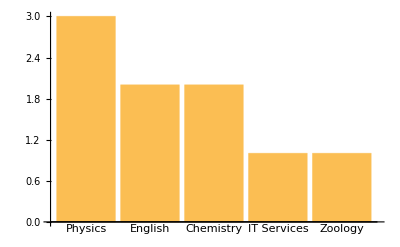

```mathematica
BarChart[{3,2,2,1,1},ChartLabels->{"Physics","English","Chemistry","IT Services","Zoology"}]
```

# Extracting Elements from Tally

The output of Tally is a nested list with the count of each item distinct in the second element of each list, the structure of the object can be visualised using TreeForm:

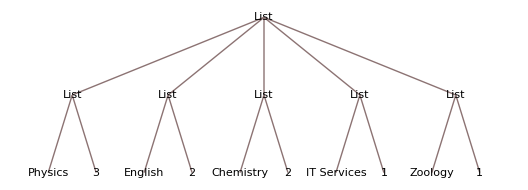

```mathematica
departmentsTally=Tally[departments];
TreeForm[departmentsTally]
```

In order to insert the output of Tally into BarChart we must be able to extract the relevant parts of the data structure:

In the Wolfram Language the n-th element of a list is the n-th element of a list, and can be extracted using the function Part:

```mathematica
Part[departments,1]
```

This is more typically written in shorthand:

```mathematica
departments[[1]]
```

It is often convenient to extract elements by negative index:

```mathematica
departments[[-1]]
```

When using Part it is useful to remember that the Wolfram Language is (at least in general) row orientated - so to extract the second column of the third element of departmentsTally the following would be evaluated:

```mathematica
departmentsTally[[3,2]]
```

2

To extract the entirety of the second column it is therefore necessary to use the operator All

```mathematica
departmentsTally[[All,2]]
```

{3,2,2,1,1}

# Using Transpose to Construct Tally like Lists

Lists are the primary data structure in the Wolfram Language, and it is crucial to understand how data can be combined together or otherwise operated on to create usefully shaped lists for visualisation and further analysis.

The Wolfram Language is designed as a very mathematically-orientated language, it’s functions are therefore typically named after the mathematical operation you are undertaking. For instance, to combine two lists into a Tally like operation you would use the function Transpose.

## Generating Data for Transpose

For the purposes of an example, let us generate some data concerning the typical RCUK grant holder. Unfortunately, the RCUK do not provide the underlying data for their diversity report (http://www.rcuk.ac.uk/RCUK-prod/assets/documents/skills/RCUKDiversityNarrativesanddata.pdf) but we can infer that the average age of a grant holder is 49.

Let’s create example profiles for these researchers, firstly by obtaining likely names for the individuals from the ONS website. The details of Import will be introduced later, but by referring to the documentation for Import it should be possible to understand the basics of this input:

```mathematica
boysNames=Import["http://www.ons.gov.uk/ons/rel/vsob1/baby-names--england-and-wales/1904-1994/top-100-baby-names-historical-data.xls",{"Data","Boys",Range[6,105],8}]
```

```mathematica
girlsNames=Import["http://www.ons.gov.uk/ons/rel/vsob1/baby-names--england-and-wales/1904-1994/top-100-baby-names-historical-data.xls",{"Data","Girls",Range[6,105],8}]
```

Lists can easily be joined together using Join:

```mathematica
grantHoldersNames=Join[boysNames,girlsNames]
```

We might be interested to know the birth months of these individuals, which we’ll assume are equally distributed through the year and can therefore be generated with RandomInteger:

```mathematica
grantHoldersBirthMonth=RandomInteger[{1,12},Length[grantHoldersNames]]
```

Thus far in the course we have only considered discretised data, however the Wolfram Language provides a huge variety of tools for generating data from continuous distributions:

```mathematica
grantHoldersHeight=RandomVariate[NormalDistribution[160,20],Length[grantHoldersNames]]
```

We could continue to generate data about these grant holders as necessary

```mathematica
grantHoldersWeight=RandomVariate[SkewNormalDistribution[75,20,5],Length[grantHoldersNames]]
```

## Transposing Data

These lists can now be combined together using Transpose:

```mathematica
grantHolders=Transpose[{grantHoldersNames,grantHolderBirthMonth,grantHoldersHeight,grantHoldersWeight}]
```

Using our knowledge of the Part function we can now visualise the distribution of birth weights using the DistributionChart function

```mathematica
DistributionChart[grantHolders[[All,3]]]
```

It is important to consider the disadvantages of combining data into nested lists in the manner - despite data being collected together about each individual it is dependent on you to remember what data each column contains. 

It may be more convenient to use Associations, as discussed later in the course.

# Exercises: Parts and BarCharts

## Department BarChart

Using the data you entered into your notebook previously build a BarChart, in case you do not have the data still at hand here is some example data:

```mathematica
departments={"Physics","English","Chemistry","IT Services","Physics","Zoology","English","Chemistry","Physics"};
monthsAtOx={5,12*3,3*12,6*12,7*12,10*12,3,8,10};
```

Your output should look something like this:

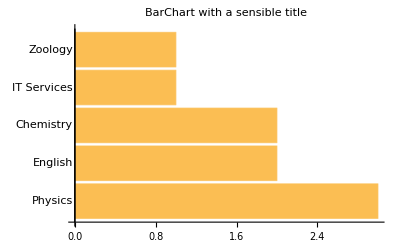

Use the Part function to build a BarChart from the output of Tally[departments]

Refer to the documentation for BarChart to find the appropriate option to achieve the following:

Add an appropriate title for the chart

Rotate the bars to run horizontally: increasing from left to right

## Years at Oxford BarChart

Create a BarChart from a Tally of the months at Oxford

Ensure that a casual reader understands the axes of the chart using appropriate Options for the Chart.

Consider whether this is the most appropriate visualisation for this continuous dataset - is there a more appropriate Chart available?

# Manipulate

It is almost trivially simple to create interactive elements in the notebook interface of Mathematica using the Wolfram Language - the “Hello World” example of an interactive element is as follows:

```mathematica
Manipulate[x,{x,1,19}]
```

The Syntax for Manipulate variables is very similar to that of Range and it’s relatives:

Generate the range 0.0, 0.2, 0.4, 0.6, 0.8, 1.0

```mathematica
Range[0,1,.2]
```

{0.,0.2,0.4,0.6,0.8,1.}

Variable x is only allows to have the values 0.0, 0.2, 0.4, 0.6, 0.8, 1.0

```mathematica
Manipulate[x,{x,0,1,0.2}]
```

Labels and default values are provided to Manipulate as follows

```mathematica
Manipulate[x,{{x,0.6,"Slider 1"},0,1,0.2}]
```

There are a variety of ControlTypes available to Manipulate:

```mathematica
Manipulate[{
sliderValue,checkboxValue,setterValue,textValue},
{{sliderValue,12,"Slider"},0,1,0.2},
{{checkboxValue,False,"Checkbox"},{True,False}},
{{textValue,"Hello World","Enter Text:"}}
]
```

# Manipulate: ListPlot

ListPlot and its relatives provide tools for visualising scatter charts and are extremely flexible:

```mathematica
ListPlot[{1,4,6}]
```

```mathematica
ListLinePlot[{{1,3},{4,7},{8,9},{10,4}}]
```

Often there is an expression that you wish to evaluate at particular points and visualise the results using ListPlot - to first generate the data one would use the Table function:

```mathematica
data=Table[i+i^2,{i,1,10}]
```

{2,6,12,20,30,42,56,72,90,110}

Manipulate then becomes a powerful tool for exploring your expression:

```mathematica
Manipulate[
ListPlot[
Table[i+i^2,{i,1,n}]
],
{n,5,8}
]
```

Conversly, Manipulate might be used for scanning through an existing dataset such as the following:

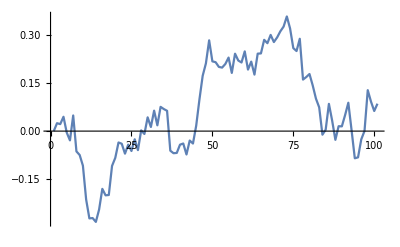

```mathematica
price=RandomFunction[WienerProcess[.3,.5],{0,1,0.01}]["Values"];
ListLinePlot[price]
```

Using the Take function an IntervalSlider can be used to effectively slice through this data:

```mathematica
Manipulate[
ListLinePlot@Take[price,foo],
{foo,IntervalSlider[#,{1,100,1}]&}
]
```

Take::normal: Nonatomic expression expected at position 1 in Take[price,{26,75}].

ListLinePlot::lpn: Take[price,{26,75}] is not a list of numbers or pairs of numbers.

# Exercises: Manipulate

## Labelling Buttons in Manipulate

The Setter ControlType of Manipulate provides the ability to label buttons with a different value to what is assigned to a variable when clicked, for insance:

```mathematica
Manipulate[
variable,
{{variable,"a","Choose a letter"},{"a"->"z","b"->"y","c"->"x"}}
]
```

Using this information attempt to build the following interface, the steps below will help you

Provide a slider for the user to select the number

Experiment with the standard arithmetic operations from Excel etc to decide how the operations listed above could be achieved

Add to the Manipulate a control that allows the operations above to be performed

Provide the control values with the appropriate labels.

## Changing Visualisations in Manipulate

In many languages it is necessary to use control structures like Switch statements to change the function applied to a series of arguments, in the Wolfram Language this can often be circumvented by changing the head of an expression in Manipulate:

```mathematica
Manipulate[
chart[{1,2,4,7}],
{chart,{PieChart,BarChart}}
]
```

Using this information attempt to build the following interface, the steps below will help you

Use ListPlot to visualise the output of the two following expressions from 0 to 20, you will need to refer to your notes on the Table function

Sin[i]/i

Sin[i]/i^2

Wrap your ListPlot inside of Manipulate and allow the user to select between Sin and Cos for the two functions

Allow the user to switch between ListPlot and ListLinePlot visualisations of the data

## Pivoting Through Data with Manipulate

Manipulate is particularly useful for providing a way to interactively pivot through your datasets, in this exercise we will build a tool that allows us to visualise the distribution of the different properties of grant holders we looked at previously:

For convenience, the code for recomputing grantHolders is provided below:

```mathematica
boysNames=Import["http://www.ons.gov.uk/ons/rel/vsob1/baby-names--england-and-wales/1904-1994/top-100-baby-names-historical-data.xls",{"Data","Boys",Range[6,105],8}];
girlsNames=Import["http://www.ons.gov.uk/ons/rel/vsob1/baby-names--england-and-wales/1904-1994/top-100-baby-names-historical-data.xls",{"Data","Girls",Range[6,105],8}];
grantHoldersNames=Join[boysNames,girlsNames];
grantHoldersBirthMonth=RandomInteger[{1,12},Length[grantHoldersNames]];
grantHoldersHeight=RandomVariate[NormalDistribution[160,20],Length[grantHoldersNames]];
grantHoldersWeight=RandomVariate[SkewNormalDistribution[75,20,5],Length[grantHoldersNames]];
grantHolders=Transpose[{grantHoldersNames,grantHoldersBirthMonth,grantHoldersHeight,grantHoldersWeight}];
```

Histogram is a new visualisation function but works similarly to other charts - create a Histogram showing the distribution of birth months in the dataset through the use of the Part function

Wrap the Histogram in Manipulate and provide buttons that allow the user to switch between the different columns of grantHolders.

Provide names to the columns following the steps in the first exercise

Allow the user to switch between Histogram, DistributionChart and Histogram

Additional Steps

Create a list of the column names

Use the function StringJoin to label the chart with “Distribution of <<columnName>> Amongst Grant Holders”. To achieve this you will benefit from using this list:

```mathematica
columnNames={"Height","Weight"};
```

# Sharing Interactive Elements

There are two mechanisms through which interactive content built with the Wolfram Language can be shared with others, including those who do not have a Mathematica licenses.

## Computable Document Format (.cdf) files

Wolfram Language notebooks may be saved as .cdf files which can then be opened by others in the freely available CDF Player (http://www.wolfram.com/cdf-player/).

It is important to understand that CDF files are runtime only - the user cannot evaluate or modify any code within the file. For this reason, any interactive elements must already have their data embedded within them.

Take for example the following interactive element:

```mathematica
list={1,3,4,5,6,7,8};
```

```mathematica
Manipulate[
ListPlot[list[[;;i]]],
{{i,2,"Elements of list to show"},1,Length[list],1}
]
```

Creating a .cdf containing only these files and opening it in CDF Player will not work as expected:

This is because the output of Manipulate does not know the value of the symbol list. There are a number of ways of solving this:

SaveDefinitions → True will ensure* that the Manipulate stores all of the necessary information for it to run

```mathematica
Manipulate[
ListPlot[list[[;;i]]],
{{i,2,"Elements of list to show"},1,Length[list],1},
SaveDefinitions->True
]
```

Initialization :> (expr;) allows the Manipulate to pre-evaluate expressions before it is displayed on screen

```mathematica
Manipulate[
ListPlot[list[[;;i]]],
{{i,2,"Elements of list to show"},1,Length[list],1},
Initialization:>(list={1,3,4,5,6,7,8};)
]
```

## Wolfram Cloud

The Wolfram Cloud is a collection of tools for using the Wolfram Language in the cloud, either as a service or so for sharing interactive content built using the language.

This is achieved very easily, by simply wrapping a Manipulate with the function CloudDeploy. Note the use of Permissions→”Public” to create a URL that can be accessed by anyone.

```mathematica
CloudDeploy[Manipulate[
DistributionChart[
Table[RandomVariate[NormalDistribution[mean^exponent,sd],25],
{mean,1,5}]
],
{sd,1,5},
{exponent,{0.8,1,1.2}}
],Permissions->"Public"]
```

CloudObject[]

A free Wolfram Development Platform is available to anyone that registers for a Wolfram Cloud account, however the Cloud is a subscription based service which is charged in terms of “compute time” for content that you develop which is used by others. “Compute time” is measured in terms of Cloud Credits.

Deliminating the Wolfram Cloud services is somewhat beyond the scope of the course, but briefly:

Wolfram Development Platform
Useful for deploying Wolfram Language applications, i.e. as an API. For example, the Wolfram Language has very powerful statistical analysis capabilities and you may wish to build a CloudAPI that allows data to be sent through for analysis and output either as a visualisation or, for instance, as JSON for consumption elsewhere.
Any computation time used by others will consume Cloud Credits.

Mathematica Online
Designed for sharing entire notebooks with a select group of individuals, for instance lecture notes for a seminar series. Nominated users of these notebooks will not consume Cloud Credits through their interaction with interactive content or evaluation of code.

# Importing Data from XLSX

The Wolfram Language implements many operations through “super functions”, importing data is a good example of this as Import is used to import all of the supported file formats:

```mathematica
$ImportFormats
```

For example purposes, we’ll export data from a Google Sheet as an .xls file. The Google Sheet contains survey results concerning how many desktop items University employees had on their work machines, it can be downloaded directly from here: https://goo.gl/cGr5kN

The expanded URL clearly has a .xlsx extension, this can be imported directly using the Wolfram Language as follows:

```mathematica
desktopItems$Import=Import["https://docs.google.com/spreadsheets/d/1dYg-w-k0upVEKhBzXCbikDN33o3pMtjPhy7Zb9E7kDg/pub?gid=651658206&single=true&output=xlsx","XLSX"]
```

The output of importing an XLSX (or XLS) file is as follows, even in the case of a single sheet workbook:

```mathematica
{sheet1,sheet2}
```

Additional information can be supplied in the second argument of the function to restrict the import to specific sheets, and columns. This was performed previously for the ONS data:

```mathematica
Import["http://www.ons.gov.uk/ons/rel/vsob1/baby-names--england-and-wales/1904-1994/top-100-baby-names-historical-data.xls",
{"XLS",(*file format*)
"Data",(*representation of data to import*)
"Boys",(*sheet name or index*)
Range[6,105],(*rows*)
8(*column*)
}]
```

The Google Sheet name isn’t meaningful in this case so let us import the first sheet by it’s index:

```mathematica
desktopItems$Import=Import["https://docs.google.com/spreadsheets/d/1dYg-w-k0upVEKhBzXCbikDN33o3pMtjPhy7Zb9E7kDg/pub?gid=651658206&single=true&output=xlsx",{"XLSX","Data",1}];
```

The following pattern is useful for extracting the column headings and data from the import:

```mathematica
desktopItems$Headers=First[desktopItems$Import];
desktopItems$Data=Rest[desktopItems$Import];
```

As before, the data can be displayed as a Grid easily to inspect the data for consistency.

```mathematica
Grid[Prepend[desktopItems$Data[[10;;15]],desktopItems$Headers],Frame->All]
```

Timestamp | How many items are there on your desktop? | What's your operating system? | Which University Department do you belong to? | Which University do you belong to?
Fri 6 Nov 2015 14:16:31GMT | 20. | Windows 7 | Electrical Engineering | University of Glasgow
Fri 6 Nov 2015 14:25:27GMT | 7 shortcuts to folders | Mac (OS X) | IT Services | University of Oxford
Fri 6 Nov 2015 14:25:53GMT | 20. | Windows 7 | IT Services | University of Oxford
Fri 6 Nov 2015 14:26:35GMT | 21. | Windows 7 | IT | University of Oxford
Fri 6 Nov 2015 14:26:35GMT | 0. | Linux | IT Services | University of Oxford
Fri 6 Nov 2015 14:26:54GMT | 0. | Linux | Nuffield Department of Population Health | Universit of Oxford

# Filtering and Cleaning Data with Patterns

The Wolfram Language provides extremely useful tools for data processing and cleansing, through the use of pattern matching through both Cases and replacement rules.

We’re going to address two issues with the second column of the data:

A user entered “7 shortcuts to folders” which we will replace with the number 7

A user entered 4384 which is an unrealistic value - this record will be removed from the dataset

## Cases

Cases is a super function for filtering data according to patterns and/or conditions, in order to use the function it is important to introduce the concept of Heads.

In the Wolfram Language every expression has a Head:

```mathematica
{Head[1],Head["1"]}
```

{Integer,String}

Cases can be used to find all elements that have a particular Head using the syntax, _Head

```mathematica
Cases[{1.,"1",4.},_Real]
```

{1.,4.}

This can be applied to the dataset above to find all elements that are Strings:

```mathematica
Cases[desktopItems$Data,{date_,number_String,os_,department_,uni_}]
```

{{Fri 6 Nov 2015 14:25:27GMT,7 shortcuts to folders,Mac (OS X),IT Services,University of Oxford}}

Cases is primarily useful where data needs to be subsetted and operated upon, however we are interested in replacing the element of the dataset - which will be achieved using replacement rules.

We can, however, use DeleteCases to remove those elements where the number of items is greater or equal to 1000:

```mathematica
desktopItems$Data=DeleteCases[desktopItems$Data,{date_,number_,os_,department_,uni_}/;number>=1000]
```

## Replacement Rules

Replacement rules are useful where elements must be modified should they meet a pattern and/or condition, they are typically implemented using the following syntax:

```mathematica
{{1.,13.,7},{1.,13.,"7 shortcuts"}}/.element_String:>StringSplit[element," "]
```

{{1.,13.,7},{1.,13.,{7,shortcuts}}}

The /. is an infix operator for the function ReplaceAll, and the symbol :> is simply :>

```mathematica
ReplaceAll[{{1.,13.,7},{1.,13.,"7 shortcuts"}},element_String:>StringSplit[element," "]]
```

{{1.,13.,7},{1.,13.,{7,shortcuts}}}

More processing of the string is required to obtain the 7 and to convert it into a Real:

The following will extract the first element of the List resultant from StringSplit

```mathematica
StringSplit["7 shortcuts"," "][[1]]
```

7

ToExpression will convert the String into an Integer:

```mathematica
ToExpression["7"]+2
```

9

These steps can then be combined to replace the string with the number 7:

```mathematica
{{1.,13.,7},{1.,13.,"7 shortcuts"}}/.element_String:>ToExpression[StringSplit[element," "][[1]]]
```

{{1.,13.,7},{1.,13.,7}}

# Exercises: Processing Data and Importing From Excel

## Tidying the Desktop Items

Use your knowledge of Parts to ensure that the row containing the string “7 shortcuts” is replaced with the number string.

You do not need to use the /. function if you choose to use another method, and you may wish to consider alternatives. One alternative may be made obvious to you through the following example. 

However, you shoud not hardcode for a specific string as this is not a flexible solution.

```mathematica
thisList={1,"this is 4",7};
thisList[[2]]=4;
thisList
```

To test whether you have succesfully completed this task the following should evaluate as True:

```mathematica
MemberQ[desktopItems$Data[[All,2]],q_?NumericQ /;q≤1000]
```

## Importing Excel Files Locally

On the desktop is folder called “Wolfram Language Example files” which contains two Excel files that requires cleaning in a similar fashion to the previously studied Excel file. However, the files must be imported from a local source.

This can be achieved by navigating in the menubar to Insert → File Path and then selecting the files individually and providing their filepaths to Import. You are encouraged to use this solution if necessary.

However, it is much more useful to be able to specify a folder location to Mathematica as the WorkingDirectory through the use of the SetDirectory function:

```mathematica
SetDirectory[$HomeDirectory]
```

/Users/martinjohnhadley

Files in the working directory can now be listed easily, and can be imported by specifying their filenames alone:

```mathematica
{Short[FileNames[]],Import["homedirectory.txt"]}
```

{{.android,Applications,.atom,.bash_history,«54»,.thumbnails,tmp.txt,.Trash,VirtualBox VMs},I was in the $HomeDirectory}

Import the two Excel files into Mathematica and store the data from the workbooks against two appropriately named symbols.

In each file there are incorrectly or suspicious, replace each of these in turn:

There are two dates incorrect typed as “45 y” - replace these using the method used above.

Gavin has an age of 333 - this is suspiciously high and impossible to decide how to fix. Remove or drop this element.

Louis has an age of -19 which is impossible but convincingly interpretable as 19. Find a method to replace any negative number (those below 0) to be replaced with their absolute value.

Michael’s age has been entered as 34y which cannot be split using a “ “ character. 
Decide on an appropriate way to treat this entry, note that the most flexible method would look for digit characters.

Join the two tables of data together into a Grid.

The output should look as follows:

Name | Age | City of Birth
Jane | 23. | Northampton
Sally | 21. | Bellyinborough
Rita | 25. | Budapest
Louis | 10. | Birmingham
James | 45 | Edinborough
Michael | 34 | Cardiff
Paul | 21. | Leicester
Richard | 45 | Johannesburg‎
Andrew | 31. | Liverpool
Zoe | 40. | Portsmouth
Marlena | 31. | Cardiff

# Associations

Thus far we have used Lists to store and operate on our data, however it can be incredibly useful to use Associations. Associations are similar to associative arrays and dictionaries found in other programming languages. They are introduced here to provide a basic introduction only.

```mathematica
assoc=<|"Key1"->1,"Key 2"->3,"This is my third key"->"data"|>;
```

Data can be accessed directly from an association using the key:

```mathematica
assoc[["Key 2"]]
```

3

The following code creates a list of associations using the function Map - it is beyond the scope of this course but is addressed in detail in the Wolfram Language programming course:

```mathematica
desktopItems$Headers={"Timestamp","Desktop Items","OS","Department","University"};
desktopItems$Associations =Map[AssociationThread[desktopItems$Headers->#]&,desktopItems$Data];
```

This structure is useful as all Desktop Items can be extracted easily:

```mathematica
desktopItems$Associations[[All,"Desktop Items"]]
```

{20.,21.,0.,0.,46.,18.,0.,2.,89.,23.,4.,81.,10.,22.,146.,99.,104.,5.,35.,0.,44.,194.,4.,28.,21.,0.,8.,7.,39.,15.,22.,31.,85.,19.,0.,0.,3.,4.,140.,27.,7.,92.,1.,137.,68.,10.,10.,113.,27.,34.,12.,22.,16.,6.,21.,54.,82.,25.,9.,17.,29.,48.,4.,9.,16.,1.,19.,198.,11.,59.,0.,15.,72.,29.,35.,38.,8.,54.,13.,24.,82.,31.,24.,84.,76.,34.,6.,0.,53.,0.,17.,110.,60.,3.,15.,7.,48.,9.,50.}

Associations allow for SQL-like queries to be written and offer a more streamlined and (computationally) faster approach to filtering data than using Cases (or /.) on a list.

The following query will select all elements where the key OS is equal to “Mac (OS X)”

```mathematica
macOS=Query[Select[#"OS"=="Mac (OS X)"&]][desktopItems$Associations]
```

Additional criteria may be added easily:

```mathematica
messyMacs=Query[
Select[
(#"OS"=="Mac (OS X)")&&
(#"Desktop Items" > 20)&]][desktopItems$Associations]
```

# Exercises: Associations

## Practicing Queries

It is useful to have example data sets to learn how functions work, use the skills learned previously to create and then filter a dataset with the following structure:

```mathematica
testAssociation={
<|"Category"->"A","Size"->10,"Users"->1021,"Interactions"->12|>,
...
}
```

Use Table to create a list of associations with 50 individuals in it, the following template will help ypu

```mathematica
Table[{{"Key 1","Value"},{"Key 2",RandomInteger[10]}},5]
```

{{{Key 1,Value},{Key 2,9}},{{Key 1,Value},{Key 2,7}},{{Key 1,Value},{Key 2,0}},{{Key 1,Value},{Key 2,4}},{{Key 1,Value},{Key 2,4}}}

Ensure your association’s keys have the following properties:

“Category” should make a random choice from {“A”,”B”,”C”,”D”}

“Size” should be a random integer between 5 and 50

“Users” should be a random variate from a NormalDistribution with a mean of 1500 and standard deviation of 400

“Interactions” should be a random variate from the following: SkewNormalDistribution[10,5,-6]

Write a query that only selects those entries where “Category” is “A” OR “B”

Write a query that selects all entries with greater than 8 “Interactions” and a “Size” greater than 11 from “Category” “C” and “D”

Tally the number of individuals in each category and display the results in a BarChart

# Going Further with the Wolfram Language

The ITLP Courses catalog currently has two courses dedicated to the Wolfram Language, with additional content planned for the future. If there are specific courses you’re interested in then please do pass on this feedback in the survey you’ll receive after this course.

Oxford provides access to Lynda.com for all staff and students; Lynda is an video learning service with a variety of content dedicated to Mathematica and the Wolfram Language.

The Wolfram company maintain a Q&A community at community.wolfram.com where users of Wolfram technologies can discuss their experiences and ask for assistance.

Stackexchange is the canonical Q&A community for programming questions, and the dedicated subsite mathematica.stackexchange.com is an excellent source of information and support in using the language and Mathematica environment.